```mathematica
(*Styling of the text*)
st[text_]:=Style[text,Directive[Large,FontFamily->"Linux Libertine Display"]];
```

```mathematica
(* approximant size *)
n=5;
```

```mathematica
(* Z^2 lattice *)
z2=Flatten[Table[{x,y},{x,0,Fibonacci[n+1]-1},{y,0,Fibonacci[n]-1}],1];
square[{x_,y_}]:=Rectangle[{x,y},{x+1,y+1}];
```

```mathematica
(* projection axis *)
cut=Line[{{0,0},{Fibonacci[n+1],Fibonacci[n]}}];
(* upper limit of the selection region *)
window=Translate[cut,{-1,1}];
```

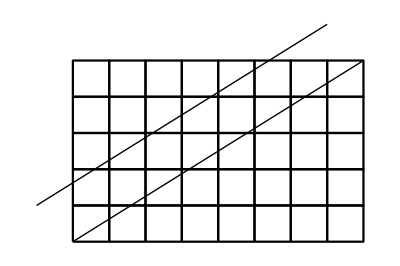

```mathematica
Graphics[{cut,window,{EdgeForm[{Thickness[0.004],Opacity[1.]}],Opacity[0],square/@z2}}]
```

```mathematica
(* enumerate the coordinates of the selected points *)
r[i_]:={Floor[i Fibonacci[n+1]/Fibonacci[n+2]],Ceiling[i Fibonacci[n]/Fibonacci[n+2]]};
```

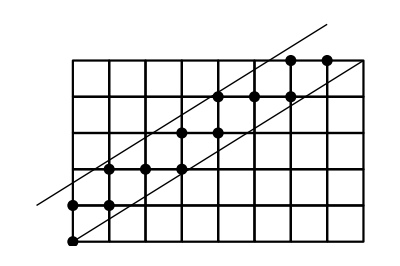

```mathematica
selPts=r/@Range[0,Fibonacci[n+2]-1];
Graphics[{{PointSize[0.02],Point[selPts]},cut,window,{EdgeForm[{Thickness[0.004],Opacity[1]}],Opacity[0],square/@z2}}]
```

```mathematica
c=Fibonacci[n+1]/√(Fibonacci[n]^2+Fibonacci[n+1]^2);
s=Fibonacci[n]/√(Fibonacci[n]^2+Fibonacci[n+1]^2);
(* projection of a selected point on the cut axis *)
proj[{x_,y_}]:={c,s}(x c + y s);
```

```mathematica
(* collection of projection pts *)
projPts=proj/@selPts;
(* collection of projection lines *)
projLines=MapThread[Line[{#1,#2}]&,{selPts,projPts}];
```

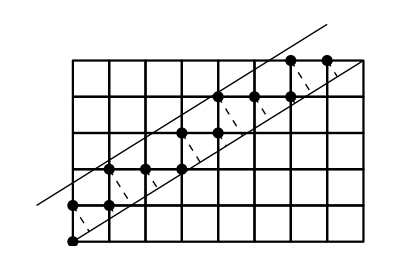

```mathematica
Graphics[{{Dashed,projLines},{PointSize[0.02],Point[selPts]},cut,window,{EdgeForm[{Thickness[0.004],Opacity[1]}],Opacity[0],square/@z2}}]
```

```mathematica
(* on the cut, alternate two types of lines *)
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
col1=comp;
col2=BostonBlue;
(* draw a little line bewteen points i and i+1 along the cut *)
(* (rf-ri)[[1]] is either 0 (short) or 1 (long) *)
cutLine[i_]:=Block[{ri=r[i],rf=r[i+1]},{Blend[{col1,col2},(rf-ri)[[1]]],{AbsoluteThickness[3],Line[{proj[ri],proj[rf]}]}}]
```

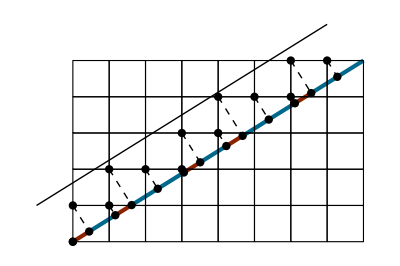

```mathematica
Graphics[{{cutLine/@Range[0,Fibonacci[n+2]-1],{Dashed,projLines},{PointSize[0.015],Point[selPts],Point[projPts]},window,{EdgeForm[{Opacity[1]}],Opacity[0],square/@z2}}}]
```

```mathematica
(* text *)
δ=0.3;
abs=Text[st@"F_n",{Fibonacci[n+1]/2,-δ-0.1}];
ord=Text[st@"F_(n - 1)",{Fibonacci[n+1]+δ+0.5,Fibonacci[n]/2}];
(* projection angle *)
ang={Text[st@"ω_n",{2.2,0.6}],Circle[{0,0},#,{0, ArcTan[Fibonacci[n]/Fibonacci[n+1]]}]&/@{1.6,1.7}};
(* couplings *)
tts=Text[st@"t_s",{4.55,2.5}];
ttw=Text[st@"t_w",{4.05,2.15}];
```

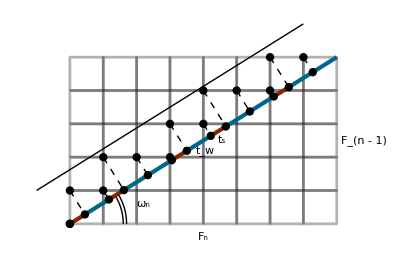

```mathematica
g=Graphics[{ang,abs,ord,{{EdgeForm[{Opacity[0.3],AbsoluteThickness[2]}],Opacity[0],square/@z2},cutLine/@Range[0,Fibonacci[n+2]-1],{Dashed,projLines},{PointSize[0.015],Point[selPts],Point[projPts]},window},tts,ttw}]
```

```mathematica
Export[NotebookDirectory[]<>"cut_and_project.pdf",g]
```

/home/nicolas/git/talks/Aperiodic 2015 Prague/cut_and_project.pdf